```mathematica
Clear[Evaluate[Context[]<>"*"]];
```

```mathematica
NotebookOpen[NotebookDirectory[]<>"calAnalysis.nb",Visible->False];
NotebookEvaluate[%];
NotebookClose[%%];
```

```mathematica
SetDirectory@NotebookDirectory[];
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
HideText["Basic utilities"]
```

Basic utilities

```mathematica
(*NotebookOpen[NotebookDirectory[]<>"calAnalysis.nb"];*)
```

```mathematica
(*NotebookClose[NotebookOpen[NotebookDirectory[]<>"calAnalysis.nb"]];*)
```

```mathematica
angleList={20,40,60,80,100,120};
rawDataScatterSet=Import["data/scatter"<>ToString[#]<>".dat.txt","Data"]⟦All,1⟧&/@angleList;
rawDataBGSet=Import["data/bg"<>ToString[#]<>".dat.txt","Data"]⟦All,1⟧&/@angleList;
rawDataSet=rawDataScatterSet-rawDataBGSet;
```

```mathematica
omarker=Graphics[{Thickness[.2],Circle[]}];
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListPlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
peaks=Select[With[{domain=#2},
IntervalMemberQ[Interval@domain,#1⟦1⟧]&]]@N@FindPeaks[#1,8]&@@@Transpose[{
rawDataSet,
{{421,441},{351,371},{272,292},{216,236},{172,192},{141,161}}
}]//Flatten[#,1]&;
peakX=%//Transpose//Extract[1]
```

{432.,362.,280.,224.,183.,152.}

```mathematica
eList=calFunction/@peakX;
eListRef={613.735,507.823,401.635,319.645,262.597,224.898};
TableForm[{angleList,eListRef,eList,(eList-eListRef)/eListRef}ᵀ]
```

20 | 613.735 | 604.071 | -0.015746
40 | 507.823 | 506.463 | -0.00267887
60 | 401.635 | 392.121 | -0.0236877
80 | 319.645 | 314.034 | -0.0175527
100 | 262.597 | 256.864 | -0.0218333
120 | 224.898 | 213.637 | -0.0500716

```mathematica
"R correction";
Interpolation[{{200,300,400,500,600,662,800,1000},
{.8841,.7236,.5875,.4912,.4266,.3914,.3373,.2977}}ᵀ]/@eList//Column;
```

```mathematica
"η correction";
Interpolation[{{100,150,200,300,400,500,600,800,1000},
{1.09,1.07,1.04,.917,.811,.737,.687,.617,.569}}ᵀ]/@eList//Column;
```

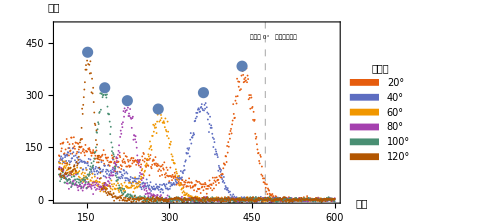

ePlot.pdf

```mathematica
ePlotRange={100,600};
ePlot=Show[ListPlot[{Range@@ePlotRange,#}ᵀ&/@(Extract[#,
Partition[Range@@ePlotRange,1]]&/@rawDataSet),
PlotTheme->"Scientific",
(*PlotMarkers->{omarker,.012},*)
PlotRange->{ePlotRange,{0,500}},
PlotRangePadding->{{0,0},{0,Automatic}},
ImagePadding->{{50,40},{25,30}},
ImageSize->Medium,
GridLines->{{474},None},
GridLinesStyle->Directive[Gray, Dashed],
(*PlotLabels->Placed[angleList,Above],*)
PlotLegends->Placed[HoldForm@Evaluate@SwatchLegend[colors,
(ToString[#]<>"°")&/@angleList,
LegendMarkerSize->6,
LabelStyle->{FontSize->8,FontFamily->"Times New Roman"},
LegendLabel->Placed["散射角",{0,1}]],
{.875,.5}]],
ListPlot[peaks,
(*Callout[#1,#2,Above,
Appearance->"Line"]&@@@{{{300,2000},"huh\nhuh"}}*)
PlotMarkers->{omarker,.04}],
Epilog->Append[
(Inset[Evaluate@Style[#1,FontFamily->"黑体",FontSize->10.5],#2]&)@@@{{"道址",Scaled[{1.075,0}]},{"计数",Scaled[{0,1.08}]}},
Inset[Style["散射角 0°   对应峰值位置",FontFamily->"黑体",FontSize->6],
Scaled[{.7665,.915}]]],
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@ePlot
```

```mathematica
SystemOpen["ePlot.pdf"]
```